# \[MathematicaIcon]25/07/17 \[MathematicaIcon]

## Tabelas

```mathematica
data=Import["C:\\Users\\Leoleo\\Desktop\\TCC\\Mathematica\\Fitting\\116.dat"];
RCtotal=Table[{data⟦i,1⟧,data⟦i,3⟧},{i,1,15}];
RCgas=Table[{data⟦i,1⟧,data⟦i,4⟧},{i,1,15}];
Erro=Table[data⟦i,5⟧,{i,1,15}];
TableForm[data,TableHeadings->{{" "},{"Raio"," ","Vtotal","Vgas","Erro"}}]
```

| Raio |   | Vtotal | Vgas | Erro
  | 0.295522 | 7.58904 | 20.94 | -0.234178 | 3.4
 | 0.985821 | 7.79329 | 39.95 | -1.95065 | 3.29
 | 1.62537 | 8.47973 | 51.54 | -1.68024 | 2.96
 | 2.18881 | 9.15955 | 67.92 | 5.43454 | 3.45
 | 3.17687 | 9.76846 | 80.22 | 13.5993 | 2.93
 | 3.76791 | 9.48569 | 83.33 | 18.0705 | 3.08
 | 4.35896 | 8.74732 | 91.38 | 21.8567 | 2.83
 | 4.8903 | 7.95629 | 101.65 | 24.2219 | 5.4
 | 6.19403 | 6.20847 | 104.77 | 27.7912 | 4.21
 | 7.16418 | 5.25717 | 108.62 | 29.5757 | 2.1
 | 8.0597 | 4.68539 | 108.48 | 30.9882 | 2.1
 | 8.95522 | 4.27244 | 108.73 | 33.3072 | 2.1
 | 9.85075 | 3.43065 | 110.24 | 36.6602 | 2.1
 | 10.7463 | 1.87414 | 110.63 | 38.4926 | 2.33
 | 11.6418 | 0.66706 | 111.52 | 36.585 | 4.74

## Equações

### Velocidade^2 Das Estrelas no Disco

```mathematica
Vdisk[r_]=((G Md (r/Rd)^2) (BesselI[0,r/(2 Rd)] BesselK[0,r/(2 Rd)]-BesselI[1,r/(2 Rd)] BesselK[1,r/(2 Rd)]))/(2 Rd);
G:=4.302/10^6;
Clear[Rd,Md];
```

### Velocidade^2 Matéria Escura

```mathematica
Vdm[r_]=(6.4 G (Po Ro^3) (1/2 Log[(r/Ro)^2+1]+Log[r/Ro+1]-ArcTan[r/Ro]))/r;
Clear[Ro,Po];
```

### Velocidade Total

```mathematica
Vtotal[r_]=√(Vdisk[r]+Vdm[r]);
Subscript[V, t][r_]=√(Vdisk[r]+Vdm[r]+Igas[r]^2);
```

## Interpolação do Gás no Disco

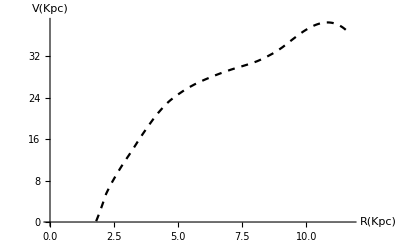

```mathematica
Igas = Interpolation[RCgas];
Gas = Plot[Igas[x],{x,1.8,11.7}, AxesOrigin->{x=0,x=0},PlotStyle->{Black,Dashed},AxesLabel->{"R(Kpc)","V(Kpc)"}]
```

## Gráfico velocidade das estrelas no disco

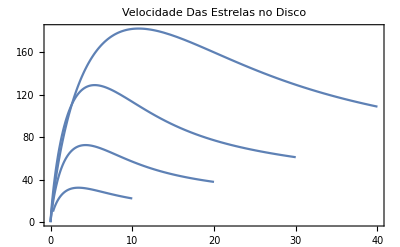

```mathematica
Vdis1=Assuming[{Rd:=10^0.2,Md:=10^9},Plot[√Vdisk[r],{r,0,10}]];
Vdis2=Assuming[{Rd:=10^0.3,Md:=10^9.8},Plot[√Vdisk[r],{r,0,20}]];
Vdis3=Assuming[{Rd:=10^0.4,Md:=10^10.4},Plot[√Vdisk[r],{r,0,30}]];
Vdis4=Assuming[{Rd:=10^0.7,Md:=10^11},Plot[√Vdisk[r],{r,0,40}]];
Clear[Rd,Md];
Show[Vdis4,Vdis3,Vdis2,Vdis1,AxesOrigin->{0,0},Frame->True,PlotLabel->"Velocidade Das Estrelas no Disco"]
```

## Gráficos das Velocidades da Matéria Escura

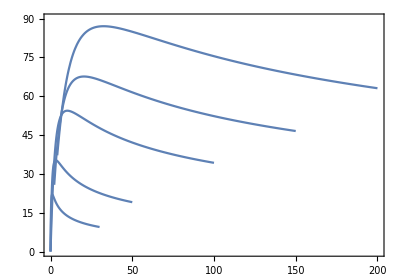

```mathematica
Vme1=Assuming[{Ro:=10^-0.5,Po:=4.1 10^8},Plot[√Vdm[r],{r,0,30}]];
Vme2=Assuming[{Ro:=1,Po:=1.05 10^8},Plot[√Vdm[r],{r,0,50}]];
Vme3=Assuming[{Ro:=10^0.5,Po:=2.5 10^7},Plot[√Vdm[r],{r,0,100}]];
Vme4=Assuming[{Ro:=10^0.8,Po:=9.7 10^6},Plot[√Vdm[r],{r,0,150}]];
Vme5=Assuming[{Ro:=10,Po:=6.4 10^6},Plot[√Vdm[r],{r,0,200}]];
Clear[Ro,Po];
Show[Vme1,Vme2,Vme3,Vme5,Vme4,PlotRange->{{0,200},{0,90}},Frame->True,AspectRatio->0.7]
Show[Vme1,Vme2,Vme3,PlotRange->{{0,15},{0,55}},Frame->True,PlotLabel->"Velocidade da Matéria Escura"];
```

## Gráfico da Curva de rotação Sem Fitting

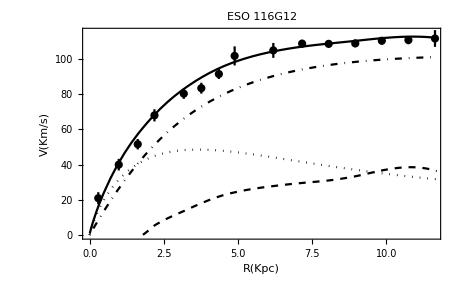

```mathematica
Needs["ErrorBarPlots`"];
Subscript[RC, total]=ErrorListPlot[{Table[{RCtotal[[i]],ErrorBar[Erro[[i]]]},{i,15}]},PlotStyle->Black];
Subscript[RC, stars]= Assuming[{Md:=2.4*10^9,Rd:=1.7},Plot[Sqrt[Vdisk[r]],{r,0,11.7},PlotStyle->{Black,Dotted}]];
Subscript[RC, halo]=Assuming[{Ro:=4.3,Po:=4.7*10^7},Plot[Sqrt[Vdm[r]],{r,0,11.7},PlotStyle->{Black,DotDashed}]];
Subscript[RC, Vtot]=Plot[Subscript[V, t][r],{r,0,11.7},PlotStyle->Black,PlotRange->Automatic];
Show[Subscript[RC, total],Subscript[RC, stars],Subscript[RC, Vtot],Subscript[RC, halo],Gas,Frame->True,PlotRange->{{0,11.6},{0,115}},PlotLabel->"ESO 116G12",FrameLabel->{"R(Kpc)","V(Km/s)"}]
Clear[Md,Rd,Ro,Po];
```